## Convert Covid-19 Cases

```mathematica
path0=NotebookDirectory[];
coviddata=Import[path0<>"covid.csv","CSV"];
days=DayCount[coviddata[[2,4]],coviddata[[-1,4]]]
cases=coviddata[[2;;,6]];
death=coviddata[[2;;,9]];
```

620

```mathematica
avgcase=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@cases[[t1+1;;t2]]],{i,0,Floor[days/5.3]}];
avgdeath=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@death[[t1+1;;t2]]],{i,0,Floor[days/5.3]}];
Export[path0<>"cases.csv",{avgcase},"CSV"];
Export[path0<>"casesD.csv",{avgdeath*1/0.0037},"CSV"];
```

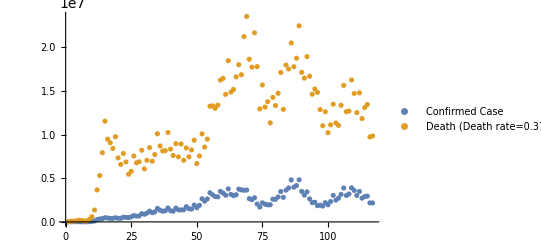

```mathematica
ListPlot[{avgcase,1/0.0037*avgdeath},PlotLegends->{"Confirmed Case","Death (Death rate=0.37%)"}]
```

## Plot TDeltaT

```mathematica
path0=NotebookDirectory[];
k = {1,2,3};totrun=100;
lineage=Import[path0<>"data/K"<>ToString[#]<>"M5E-05.out","CSV"]&/@k;
lineageA=Import[path0<>"data/K"<>ToString[#]<>"M5E-05A.out","CSV"]&/@k;
```

```mathematica
(*Functions*)
TDeltaT[lineage_,n_]:=
Module[{t0},
t0=lineage[[1]];
{t0,lineage[[n+1]]}
]
getDeltaT[lineagelist_,n_]:=TDeltaT[#,n]&/@lineagelist
```

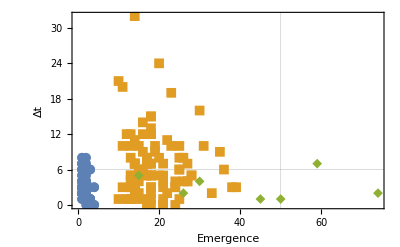

-Graphics3D-

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

{TDeltaTk1,TDeltaTk2,TDeltaTk3}=getDeltaT[#,1]&/@lineage;
ListPlot[{TDeltaTk1,TDeltaTk2,TDeltaTk3},PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]

Histogram3D[{TDeltaTk1,TDeltaTk2,TDeltaTk3,actual},Automatic,"Probability",ChartLabels->Placed[{"k=1","k=2","k=3","Real"},Above,"Framed"]]
```

```mathematica
{TDeltaTk1A,TDeltaTk2A,TDeltaTk3A}=getDeltaT[#,1]&/@lineageA;
ListPlot[{TDeltaTk1,TDeltaTk2,TDeltaTk3},PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]

Histogram3D[{TDeltaTk1,TDeltaTk2,TDeltaTk3,actual},Automatic,"Probability",ChartLabels->Placed[{"k=1","k=2","k=3","Real"},Above,"Framed"]]
```

-Graphics-

-Graphics3D-